Maxwell-Boltzmann distribution

Following cell will calculate the distribution of electron energies based on Maxwell-Boltzmann distribution

```mathematica
k=3.166811563×10^-6;(*boltzmann constant in hartree units*)
T=;(*temperature in kelvin*)
n=;(*number of electrons*)
energy[x_]:=(2π n)/(π k T)^(3/2)√x ⅇ^(-x/(k T))(*function of maxwell-boltzmann distribution*)
Plot[energy[x],{x,0,0.4}](*plots maxwell-boltzmann distribution*)
Integrate[energy[x],{x,0,∞}] (*integreates maxwell-boltzmann distribution, make sure final result is same as number of electrons*)
```

Fermi-Dirac distribution

Following cell will calculate the fermi energy at various temperatures. If your result is complex then use only the real part as the value of the fermi energy.

```mathematica
k=3.166811563×10^-6;(*boltzmann constant in hartree units*)
T=;(*temperature in kelvin*)
n=;(*number of electrons*)
V=;(*volume in hartree units*)
h=2π;(*in Hartree units h=2π*)
m=1;(*in Hartree units m=1*)
Solve[n/V==π/2((8m)/h^2)^(3/2)Integrate[x^(1/2)/(ⅇ^((x-f)/(k T))+1),{x,0,∞}],f ]
```

```mathematica
k=3.166811563×10^-6;(*boltzmann constant in Hartree units*)
T=;(*temperature in kelvin*)
n=;(*number of electrons*)
V=;(*volume in hartree units*)
h=2π;(*in Hartree units h=2π*)
m=1;(*in Hartree units m=1*)
fermi=;(*paste above result for fermi energy here*)
Print["Fermi energy in au=",fermi]
Print["Fermi energy in eV=",fermi×27.211396 ]
Print["Fermi energy in Kelvin=",fermi/k]
energy[x_]:=π/2((8m)/h^2)^(3/2)(V x^(1/2))/(ⅇ^((x-fermi)/(k T))+1);(*function of fermi-dirac distribuiton*)
Plot[energy[x],{x,0,2}](*plots fermi-dirac distribuiton*)
NIntegrate[energy[x],{x,0,∞} ](*make sure integration is same as electron count*)
```

```mathematica
NDSolve[{y'[x]==π/2((8m)/h^2)^(3/2)(V x^(1/2))/(ⅇ^((x-fermi)/(k T))+1)&&y'[0]==0},y,{x,0,∞}](*gives the functional form of the integral of the fermi-dirac distribution*) (*using NDSolve instead of InterpolatingFunction[NIntegrate] provides superior result*) (*Once solution is give you must use drop down menu to select "get solution" then use drop down menu again to select "evaluate at point..." and type in x as the point. This will generate the function as the expression "%N[x]" where N is some number based on the output in your Mathematica kernel. You will need to use this expression in the next cell to get your electron energies based on the fermi-dirac distribuiton*)
```

Finding the energy value of each electron from my chosen distribution

*Set up compute node on LC machine before running any of the following cells*

*For use with interpolating function based on numerical integration*

```mathematica
(*If using Fermi-Dirac distribution then use this cell to find energy values for each electron*)
(*This cell will run the calculation in parallel so make sure you are set up to do this before execution of calculation*)
(*This cell will find the upper limit that gives the definite integral the value of each integer from 0 to n-1 then take the average i and i+1 to get evergy value of the ith electron*)
(*Since the integral used in this cell is a Interpolated function we cannot accurately predict the upper bound that gives the result n. Therefore, to find this you will need to use the calculation in the next cell*)
solutions=a/.Parallelize[Table[Quiet[Solve[%235[a]-%235[0]==i,a]],{i,0,n-1}]];
diffs=Parallelize[Table[(solutions[[i+1]]+solutions[[i]])/2,{i,n-1}]];
DiscretePlot[energy[x],{x,Flatten[diffs]},Joined->False,Filling->None,ImageSize->Full]
Column[Flatten[diffs]]
```

```mathematica
(*This cell will give value of the final electron using the Interpolated function found via numerical integration. Make the constant the loweset possible value that still allows for the top limit to be found*)
constant=0.00004;
bottomlim=bxx/.Solve[%235[bxx]-%235[0]==n-1,bxx];
toplim =txx/.Solve[%235[txx]-%235[0]==n-constant,txx];
(toplim+bottomlim)/2
```

*For use with full analytical integration*

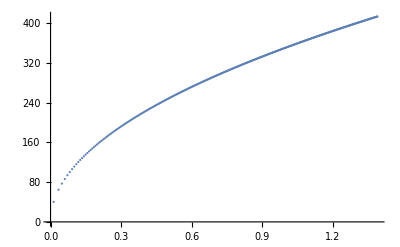

0.013162
0.0340554
0.0482715
0.0605443
0.0716522
0.081946
0.0916239
0.100812
0.109597
0.118041
0.126193
0.134089
0.141758
0.149225
0.156509
0.163628
0.170594
0.177421
0.184119
0.190697
0.197163
0.203525
0.209789
0.215961
0.222046
0.228049
0.233973
0.239823
0.245603
0.251316
0.256964
0.262551
0.268079
0.273551
0.278968
0.284334
0.289649
0.294916
0.300136
0.305311
0.310443
0.315533
0.320581
0.325591
0.330562
0.335496
0.340394
0.345257
0.350086
0.354882
0.359646
0.364378
0.36908
0.373752
0.378396
0.38301
0.387597
0.392158
0.396691
0.401199
0.405682
0.41014
0.414575
0.418985
0.423373
0.427737
0.43208
0.436401
0.440701
0.444979
0.449238
0.453476
0.457694
0.461893
0.466074
0.470235
0.474378
0.478503
0.482611
0.486701
0.490774
0.49483
0.498869
0.502892
0.506899
0.510891
0.514867
0.518827
0.522773
0.526704
0.53062
0.534521
0.538409
0.542282
0.546142
0.549988
0.553821
0.55764
0.561447
0.56524
0.569021
0.57279
0.576546
0.58029
0.584021
0.587741
0.59145
0.595146
0.598831
0.602505
0.606168
0.60982
0.61346
0.61709
0.62071
0.624318
0.627917
0.631505
0.635083
0.638651
0.642209
0.645757
0.649295
0.652824
0.656344
0.659853
0.663354
0.666845
0.670328
0.673801
0.677265
0.680721
0.684167
0.687605
0.691035
0.694456
0.697868
0.701273
0.704669
0.708057
0.711436
0.714808
0.718172
0.721528
0.724876
0.728216
0.731549
0.734875
0.738192
0.741503
0.744806
0.748101
0.751389
0.754671
0.757945
0.761212
0.764472
0.767725
0.770971
0.774211
0.777443
0.780669
0.783888
0.787101
0.790307
0.793507
0.7967
0.799887
0.803067
0.806241
0.809409
0.812571
0.815727
0.818876
0.82202
0.825157
0.828289
0.831415
0.834534
0.837648
0.840756
0.843859
0.846956
0.850047
0.853132
0.856212
0.859286
0.862355
0.865419
0.868477
0.871529
0.874577
0.877619
0.880656
0.883687
0.886713
0.889735
0.892751
0.895762
0.898768
0.901768
0.904764
0.907755
0.910741
0.913723
0.916699
0.91967
0.922637
0.925599
0.928556
0.931509
0.934456
0.9374
0.940338
0.943272
0.946202
0.949126
0.952047
0.954963
0.957874
0.960781
0.963684
0.966582
0.969476
0.972366
0.975251
0.978132
0.981009
0.983882
0.98675
0.989615
0.992475
0.995331
0.998183
1.00103
1.00387
1.00671
1.00955
1.01238
1.01521
1.01803
1.02085
1.02367
1.02648
1.02929
1.0321
1.0349
1.03769
1.04049
1.04328
1.04606
1.04884
1.05162
1.0544
1.05717
1.05994
1.0627
1.06546
1.06822
1.07097
1.07372
1.07647
1.07921
1.08195
1.08468
1.08741
1.09014
1.09287
1.09559
1.09831
1.10102
1.10374
1.10645
1.10915
1.11185
1.11455
1.11725
1.11994
1.12263
1.12531
1.128
1.13068
1.13335
1.13602
1.13869
1.14136
1.14402
1.14669
1.14934
1.152
1.15465
1.1573
1.15994
1.16258
1.16522
1.16786
1.17049
1.17312
1.17575
1.17837
1.181
1.18362
1.18623
1.18884
1.19145
1.19406
1.19667
1.19927
1.20187
1.20446
1.20705
1.20964
1.21223
1.21482
1.2174
1.21998
1.22255
1.22513
1.2277
1.23027
1.23283
1.2354
1.23796
1.24051
1.24307
1.24562
1.24817
1.25072
1.25326
1.25581
1.25835
1.26088
1.26342
1.26595
1.26848
1.27101
1.27353
1.27605
1.27857
1.28109
1.2836
1.28611
1.28862
1.29113
1.29364
1.29614
1.29864
1.30113
1.30363
1.30612
1.30861
1.3111
1.31359
1.31607
1.31855
1.32103
1.3235
1.32598
1.32845
1.33092
1.33339
1.33585
1.33831
1.34077
1.34323
1.34569
1.34814
1.35059
1.35304
1.35549
1.35793
1.36037
1.36281
1.36525
1.36769
1.37012
1.37255
1.37498
1.37741
1.37983
1.38226
1.38468
1.3871
1.38951

```mathematica
(*If using Maxwell-Boltzmann distribution then use this cell to find energy values for each electron*)
(*This cell will run the calculation in parallel so make sure you are set up to do this before execution of calculation*)
(*Since this cell uses a fully analytical integration we will be able to get the energy value for all n electrons. Each value is the average of the upper and lower limit as selected in the same method as the previous cell*)
solutions=a/.Parallelize[Table[Quiet[Solve[Integrate[energy[x],{x,0,a}]==i,a]],{i,0,n}]];
diffs=Parallelize[Table[(solutions[[i+1]]+solutions[[i]])/2,{i,n}]];
DiscretePlot[energy[x],{x,Flatten[diffs]},Joined->False,Filling->None,ImageSize->Full]
Column[Flatten[diffs]]
```